# Examining the Effects of Randomly Generated Weights and Biases on Distributions of Outputs of Untrained Neural Networks

## Abstract

## Introduction

Neural networks are one of the most researched topics in academia today and for good reason. They show promise in countless fields, ranging from control mechanisms for autonomous vehicles to the analysis of medical images to models that can outperform top players in games like chess. Inspired by the human brain, their structure is defined by multiple layers of neurons, in which each neuron processes input data from the previous layer, implements some function on the data, and passes on the output data to the next layer. Perhaps the most important part of these models are the weights and biases. Weights multiply inputs, thereby controlling the influence any given part of an input has on the activation of a give-n neuron, and biases are added to this product (allowing each neuron to output a different range of values independently from the input).

This project examines the influence of weights on the outputs of an untrained neural network. By initializing weights from different

## Background Information

## Why Examine Untrained Neural Networks?

### Effect on Training

### Initializing Weights and Biases

### Different Types of Distributions

```mathematica
initializations={{"Normal","",NormalDistribution[],"The normal distribution is the classic probability distribution. It's continuous, centered around its mean, μ, with a standard deviation, σ."},{"Gamma","",GammaDistribution[1,1],"The gamma distribution is another continuous probability distribution with two parameters. Instead of μ and σ, the Gamma distribution works with α, the shape parameter, and β, the rate parameter. Note that both of these parameters must be"},{"Uniform","",UniformDistribution[{-1,1}],"The uniform distribution is yet another continuous distribution, however it differs from both the Normal and Gamma distributions in that all outcomes are equally likely within the range of the function."}};
distributionPlots=Function[{init},{init[[1]],init[[2]],Plot[PDF[init[[3]],x],{x,-3,3},PlotLabel->init[[1]],PlotRange->All,Frame->True,FrameTicks->None],init[[4]]}]/@initializations;
initializationGrid=Grid[Prepend[distributionPlots,{"Distribution","Formula","Graph","Description"}],Frame->All,Alignment->{Center,Center}];
initializationGrid
```

This code generates a grid explaining the different types of distributions that this project will use to generate weights from, with their formulas and graphs.

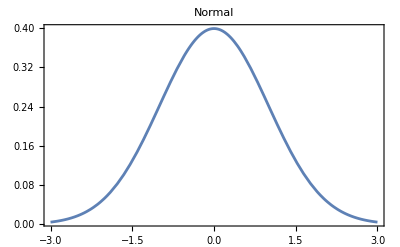
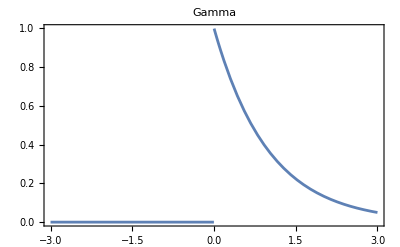
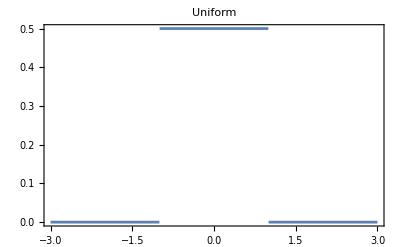
Distribution | Formula | Graph | Description
Normal |  | -Graphics- | The normal distribution is the classic probability distribution. It's continuous, centered around its mean, μ, with a standard deviation, σ.
Gamma |  | -Graphics- | The gamma distribution is another continuous probability distribution with two parameters. Instead of μ and σ, the Gamma distribution works with α, the shape parameter, and β, the rate parameter. Note that both of these parameters must be
Uniform |  | -Graphics- | The uniform distribution is yet another continuous distribution, however it differs from both the Normal and Gamma distributions in that all outcomes are equally likely within the range of the function.

An important note: The graphs of these distributions were generated with a run of the distribution using “standard parameters”: in the case of a Normal distribution; μ = 0 and σ = 1, in the case of a Gamma distribution; α = 1 and β = 1, and in the case of a Uniform distribution; range = 1.

## Linear Activation Functions

### Linear Regression

When we create a neural network with each layer having a fully linear activation function (LinearLayer), each layer simply outputs a linear combination of the outputs of the previous layer. Mathematically, this shows itself as 

Layer Output 

where  is a matrix of weights and  is the value of the bias. It’s important to note that you could apply this operation infinite times and the output would still be a linear combination of the original weights and biases. Because of this property of linear transformations, a neural network with solely linear activation functions, or in other words: only linear layers, becomes a linear regression model. This portion of the project will examine how changes in the distributions of weights and biases affect the outputs of a linear regression neural network and how the behavior changes with varying depths.

### Creating Output Plots for Linear Regression Models

```mathematica
LinearRegressionNetworkPlot[depths_,distributionType_,params_]:=Module[{netInit,f,plots,depth,distribution,title},distribution=Switch[distributionType,"Normal",NormalDistribution[params[[1]],params[[2]]],"Uniform",UniformDistribution[{-params[[1]],params[[1]]}],"Gamma",GammaDistribution[params[[1]],params[[2]]],_,NormalDistribution[0,1]];
SeedRandom[1234];
title="Outputs of Linear Regression Network with Weights initialized from a "<>distributionType <> " distribution";
plots=Table[With[{netInit=NetChain[Append[Catenate@Table[{3,LinearLayer[3]},depth],LinearLayer[1]],"Input"->{3}]},Column[{Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->distribution},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[{x,x,x}];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None],Style["depth = "<>ToString[depth],Italic,12,Gray]}]],{depth,depths}];
Column[{Style[title,Bold,14],Row[Riffle[plots,Spacer[20]]]}]]
```

This function generates plots of outputs for 15 runs of initialized neural networks with inputted depth that have weights generated from an inputted distribution (either Normal, Gamma, or Uniform), and based on the distribution type, takes either one or two parameters for generating the distribution (for a normal distribution this would be σ, for a gamma distribution it would be α and β, and for a uniform distribution it would be the range). It then plots the outputs of each run of the neural network for each of the inputted depths, showing a clear progression of the complexity of outputs as depth increases and providing visual warnings of gradient loss or explosion. Note that in this structure, each linear layer of the neural network takes in a 3-dimensional vector (used because this is the standard), and the final layer outputs a one-dimensional vector for the result of the entire neural network.

### The Effect of Depth on Output Complexity

```mathematica
Rasterize[Column[{LinearRegressionNetworkPlot[Range[8],"Normal",{0,1}], LinearRegressionNetworkPlot[Range[8],"Gamma",{1,1}],LinearRegressionNetworkPlot[Range[8],"Uniform",{1}]}]]
```

-Graphics-

Plotting the output graphs for depths 1 through 10 (using a standard normal distribution for purposes of familiarity and ease of computation) shows almost no correlation between the depth of the network and the complexity of the outputs. In fact, running this with different random seeds produces very different output graphs, where different depths produce outputs of completely different shapes with no clear trend between said shapes. This is largely explained from the earlier referenced property of linear transformations where multiple linear transformations combine to create a single, slightly different linear transformation. This means that without a non-linear activation function, the network is unable to learn many of the patterns in training data and this greatly impedes the effectiveness of the model. In other words, any arbitrarily large neural network will only linear layers behaves like a neural network with just one linear layer.

Another interest aspect of the plots above comes in the difference between the shapes of the output graphs of the neural networks generated by a gamma distribution versus the output graphs of the neural networks generated by a normal or uniform distribution. This difference is caused by the definition of the distributions: while normal and uniform distributions can take upon negative values, a gamma distribution is restricted to producing strictly nonnegative values. This means that without negative weights, the neural network generated from a gamma distribution contains only positive or zero weights and produces negative outputs for negative input values and positive outputs for positive input values. In other words, the slope of all of the output graphs for gamma distribution are always positive.

### Interactive Visualization for the Effect of Different Parameters on Output Graphs

```mathematica
Manipulate[Module[{netInit,f,plots,title,net,distribution},title="Outputs of Linear Regression Network with Weights initialized from "<>distributionType<>" Distribution";
distribution=Which[distributionType=="Normal",NormalDistribution[0,stdDev],distributionType=="Gamma",GammaDistribution[alpha,beta],distributionType=="Uniform",UniformDistribution[{-range,range}]];
netInit=NetChain[Append[Catenate@Table[{3,LinearLayer[3]},depth],LinearLayer[1]],"Input"->{3}];
plots=Table[net=NetInitialize[netInit,Method->{"Random","Weights"->distribution},RandomSeeding->seed];
f[x_?NumericQ]:=net[{x,x,x}];
SetAttributes[f,Listable];
Plot[f[x],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None,PlotStyle->ColorData[1][seed]],{seed,1,15}];
Column[{Style[title,Bold,14],Show[plots,PlotLegends->"Expressions"],Style["depth = "<>ToString[depth],Italic,12,Gray]}]],{{distributionType,"Normal","Distribution Type"},{"Normal","Gamma","Uniform"}},{{depth,1,"Depth"},1,10,1},{{stdDev,1,"Standard Deviation"},0.5,5,0.5,Appearance->If[distributionType=="Normal","Open","None"]},{{alpha,1,"Alpha (Gamma)"},0.5,5,0.5,Appearance->If[distributionType=="Gamma","Open","None"]},{{beta,1,"Beta (Gamma)"},0.5,5,0.5,Appearance->If[distributionType=="Gamma","Open","None"]},{{range,1,"Range (Uniform)"},0.5,5,0.5,Appearance->If[distributionType=="Uniform","Open","None"]}]
```

This interactive visualization comes from a very useful function in the Wolfram language, Manipulate, that allows the user to set up a function and run it for different changing parameters. The function creates a dynamic output that is displayed on the screen and changes every time the user shifts one of the parameters of the function. In this case, the function I’m using Manipulate with is a NetInitialize function that initializes a neural network with “depth” hidden layers, and weights generated from either a Normal, Gamma, or Uniform distribution. I set up the Manipulate function in a way that I could change the depth on a slider from 1 to 10 and select either Normal, Gamma, or Uniform as the distribution. Once one of these distributions have been selected, I can modify the parameters that correspond with that function using sliders (σ for the Normal distribution, α and β for the Gamma distribution, and range for the uniform distribution).

What is the point of going to the trouble of making a function like this instead of just manually changing the parameters each time we call the function? Having a dynamically updating output is actually invaluable in an exploration project such as this one, because it makes it far easier to detect patterns in output graphs and provides a method of testing different parameters that is far more efficient than repeated calls to a function (especially one like NetInitialize) that requires a fairly significant amount of runtime

## One Non-Linear Activation Function

The addition of a non-linear activation function to a neural network composed of linear layers renders the earlier property about linear transformations combining to create other linear transformations irrelevant. Because these activation functions are non-linear, iterating them upon each other results in much more complex relations than simply another version of the activation function. This allows these types of models to understand and replicate more complex relationships within training data and allows the model to attain a much higher level of fitting.

This portion of the project will examine how changes in the distribution of weights and the depth of the neural network affect the output of a given neural network. While this may seem almost identical to the previous portion, there are key differences when non-linear functions are introduced (namely the depth will actually play a role in the complexity of the output graphs). Additionally, because of this new affecting variable, we have to consider the phenomena that are gradient loss and gradient explosion. Gradient loss occurs when gradient get pushed toward 0 as they’re passed through the hidden layers of the neural network, and this is a problem because that mean the neural network is unable to learn, leading to long training times, stagnation in the performance of the neural network as a whole, and underfitting. Gradient explosion, on the other hand, is almost the exact opposite; gradients grow out of control as they’re passed through the hidden layers, and by the time they reach the last layer, they can become so large that they update the weights too drastically and cause oscillations during training. Like gradient loss, gradient explosion can result in long training times, but it leads more often to overfitting rather than underfitting.

Further sections of this portion of the project will define functions to help identify when gradient loss or gradient explosion are occurring and how to initialize the neural network in a manner that mitigates the issues.

### Activation Functions

While there are countless activation functions that can be implemented within a neural network, this project will make use of five of the most popular, selected because they provide an opportunity to compare the effects of different characteristics of activation function (e.g. fully non-linear vs piecewise linear, limited range of output vs non-limited range of output, periodic vs aperiodic, etc). These functions have been outlined in a grid below.

```mathematica
Grid[{{"Activation Function","Formula","Graph","Description"},{"Ramp (ReLU)","{
     ,
     
}
",Plot[Max[0,x],{x,-2,2},PlotLabel->"ReLU"],"Ramp outputs zero for negative values and zero, but outputs x for positive values, making it a piecewise linear function."},{"Tanh","",Plot[Tanh[x],{x,-2,2},PlotLabel->"Tanh"],"Tanh takes inputs and maps them to the range (-1, 1), and it's symmetric around the origin, so negative inputs produce negative outputs and positive inputs produce positive outputs."},{"Sin","",Plot[Sin[x],{x,-2 Pi,2 Pi},PlotLabel->"Sin"],"Sin outputs sin(x) for any input x."},{"Sigmoid","",Plot[1/(1+Exp[-x]),{x,-6,6},PlotLabel->"Sigmoid"],"Sigmoid is very similar to tanh in shape, but the key difference is that it maps input values to the range (0, 1) instead."},{"Threshold","{
     ,
     
}",Plot[If[x>0,1,0],{x,-2,2},PlotLabel->"Threshold"],"The thresholding function I've defined here outputs 1 if the input is positive and 0 otherwise."}},Frame->All,Alignment->{Center,Center}]
```

This piece of code outputs a grid containing each activation function, its formula, its graph, and a short description of it (arranged in this format for the benefit of the reader).

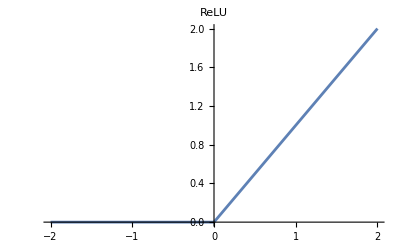
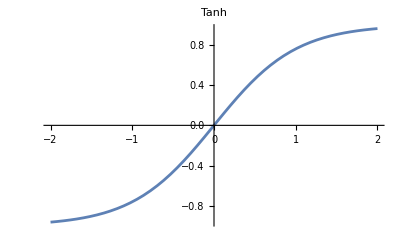
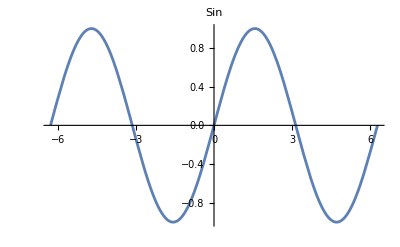
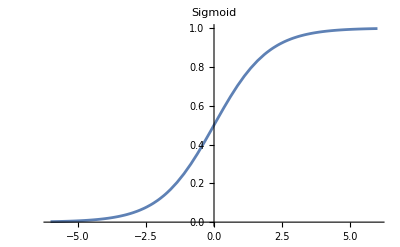
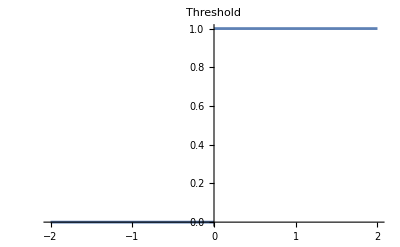
Activation Function | Formula | Graph | Description
Ramp (ReLU) | {
     ,
     
}
 | -Graphics- | Ramp outputs zero for negative values and zero, but outputs x for positive values, making it a piecewise linear function.
Tanh |  | -Graphics- | Tanh takes inputs and maps them to the range (-1, 1), and it's symmetric around the origin, so negative inputs produce negative outputs and positive inputs produce positive outputs.
Sin |  | -Graphics- | Sin outputs sin(x) for any input x.
Sigmoid |  | -Graphics- | Sigmoid is very similar to tanh in shape, but the key difference is that it maps input values to the range (0, 1) instead.
Threshold | {
     ,
     
} | -Graphics- | The thresholding function I've defined here outputs 1 if the input is positive and 0 otherwise.

These are the functions the remainder of this project will repeatedly reference, and as can be seen above they have distinct defining characteristics that make them so “interesting” for us to study.

### Testing Parameters for Normal Distributions

We’ll start with generating weights from a basic Normal distribution. With this distribution, we’ll be examining the effect of changing the standard deviation and network depth on the complexity of graphs of outputs.

```mathematica
normalNetworkPlot[activations_,depths_,sigma_]:=Module[{netPlots,netInit,f,plots,act,depth},netPlots={{"[◼]", "NetGraphPlot"}}[NetChain[Append[Catenate@Table[{3},#],{}],"Input"->"Real"],EdgeStyle->GrayLevel[.3,.5],EdgeShapeFunction->"Line",ImageSize->Tiny,AspectRatio->1/2]&/@Range[Length[depths]];
SeedRandom[1234];
plots=Append[Prepend[netPlots,""]]@Table[Prepend[Text[act/. Function[x,If[x>0,1,0]]->"Threshold"]]@Table[With[{netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act]},depth],{}],"Input"->"Real"]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->NormalDistribution[0,sigma],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths}],{act,activations}];
Grid[plots]
]
```

This function takes in parameters for a list of activation functions, a list of depths, and a standard deviation. It uses these parameters to generate a grid that consists of the plots of 15 neural networks (made up of a linear layer and  layers of activation functions where  represents the inputted depth. that had weights randomly initialized from a normal distribution with μ = 0 and the inputted σ. These outputs are for  from -3 to 3 and are intended to provide a visual representation of the behavior of an untrained neural network. Why is this useful? The behavior of the untrained neural network is what will dictate the speed and stability of the training process. In this case, we want to avoid extremes, as overly “messy” graphs can result in gradient explosion and a very unstable training process, while very flat graphs can result in gradient loss and a halt in training.

```mathematica
Rasterize[normalNetworkPlot[{Function[x,If[x>0,1,0]],Ramp,Tanh,Sin,LogisticSigmoid},{1,2,3,4},1]]
```

-Graphics-

From the graphs of the outputs, we can see a result that, for the most part, seems to have been obvious. The non-linear functions Sin and Tanh retain a fairly high frequency in their graphs, and this frequency only increases as the depth increases. From this we can tell that perhaps having too many layers with non-linear activation functions isn’t a good idea as it could quickly lead to model instability. On the other hand, the piecewise linear functions Ramp and Threshold exhibit almost the exact opposite behavior. Starting out almost as complicated as Sin and Tanh, they quickly dwindle in frequency as the network depth increases, and this can be attributed to the fact that for Threshold, as more layers are added, the outputs become either 0 or 1, and there is little variation in outputs for different inputs. For Ramp, we see that the graphs don’t ever lose all of their character, instead seemingly reaching a kind of “asymptote of flatness”, in which the graphs remain a bit too smooth for robust training but workable. The real outlier here is Logistic Sigmoid. Why does a non-linear function reach full flatness before either of the linear activation functions? Sigmoid is limited to producing outputs between 0 and 1, and a cursory glance at the function’s graph shows us that it’s first derivative rapidly approaches 0 at extreme values, whether those be positive or negative. Repeatedly applying this function over multiple layers pushes outputs toward these extrema and results in a complete loss of gradient that stops training entirely, highlighting a problem with the Logistic Sigmoid activation function (one that can be tackled with specialized initializations that will be covered later in this project!).

### Optimal Standard Deviation for Varying Network Depths and Activation Functions

The output plots above showed a problem with initialization for certain activation functions. To limit the scope of this problem, this project will explore functions to optimize the standard deviation. What is the “optimal” standard deviation? In this case, it’s the standard deviation, σ, that creates a normal distribution with mean μ and standard deviation σ that initializes weights such that depth before gradient loss or gradient explosion occurs is maximized, leading to stable training.

```mathematica
normalInitializeNet[stdDev_,activation_,depth_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},depth],{}],"Input"->"Real"],Method->{"Random","Weights"->NormalDistribution[0,stdDev],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
```

Nothing special here; we’re just initializing a Neural Network with parameters for the activation function, network depth, and standard deviation of the distribution of weights.

```mathematica
normalEvaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
```

This is the function used to evaluate outputs of the neural network (important because we’re trying to measure and plot the “smoothness” of the outputs.

```mathematica
stdDevs=Range[0.5,10,0.5];
normalMeasureVariance[activation_,depth_]:=Table[With[{netInit=normalInitializeNet[stdDev,activation,depth]},{stdDev,Mean[Table[Module[{outputs=normalEvaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]}],{stdDev,stdDevs}];
normalMeasureVarianceplotted[activation_,depth_]:=Table[With[{netInit=normalInitializeNet[stdDev,activation,depth]},Mean[Table[Module[{outputs=normalEvaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]],{stdDev,stdDevs}];
```

These two functions have almost identical functionalities, with the only difference coming in the structure of their outputs. They first take in inputs for activation function and depth and run normalInitializeNet with a neural net of that structure for each of the standard deviations in the list stdDevs, with 15 runs per initialization (to have a large enough sample size). With these outputs they run normalEvaluateNet from -3 to 3 with a step size of 0.01 (in order to try to emulate a continuous variable), and then measure the variance of the list of outputs. The difference in the functions is that normalMeasureVariance returns paired values for standard deviation and mean variance in the format {std deviation, mean variance}, while the normalMeasureVarianceplotted only returns values for the mean variance. This difference is because of the functionalities of the next two defined functions. The require different input structures, and each call upon either normalMeasureVariance or normalMeasureVarianceplotted.

```mathematica
normalOptimalStdDev[activation_,depth_]:=Module[{varianceMeasures,minStdDev,maxStdDev},varianceMeasures=normalMeasureVariance[activation,depth];
minStdDev=First[varianceMeasures[[First[Ordering[varianceMeasures[[All,2]],1]]]]];
maxStdDev=First[varianceMeasures[[First[Ordering[varianceMeasures[[All,2]],-1]]]]];
{minStdDev,maxStdDev}];
```

This normalOptimalStdDev function takes the paired outputs from normalMeasureVariance for a specific activation function and depth, orders them in ascending and descending order, and then returns a pair of standard deviation where the first one is the standard deviation that minimizes the average variance for a neural network composed of the inputted activation function and neural network depth, while the second one is the one that maximizes it.

```mathematica
depth=3;
activation=LogisticSigmoid;
normalOptimalStdDev[activation,depth]
```

{1.5,7.5}

An example running of normalOptimalStdDev shows that a standard deviation of 0.5 maximizes the average variance, while a standard deviation of 8.5 maximizes it. With the activation function, Logistic Sigmoid, the issue is almost always gradient loss rather than explosion, so we are more concerned with the maximizing value and will want to initialize the network from a normal distribution with μ = 0 and σ = 7.5.

```mathematica
normalPlotVariance[activation_,depth_,color_,title_]:=Module[{averageVarianceMeasures},averageVarianceMeasures=normalMeasureVarianceplotted[activation,depth];
ListLinePlot[Transpose[{stdDevs,averageVarianceMeasures}],Frame->True,FrameLabel->{"Standard Deviation","Average Variance Measure"},PlotLabel->title,PlotStyle->Thick,Mesh->All,MeshStyle->color,ImageSize->Large]];
```

This normalPlotVariance function plots the mean variances against the standard deviations for a certain activation function and depth. In addition to providing a visual representation of the normalOptimalStdDev function, it shows the trend in mean variance with increasing standard deviation , and we can see that while there is some variation (due to the randomness and relatively small sample size of 15 runs per neural net), the general trend is clearly upward for increasing standard deviation

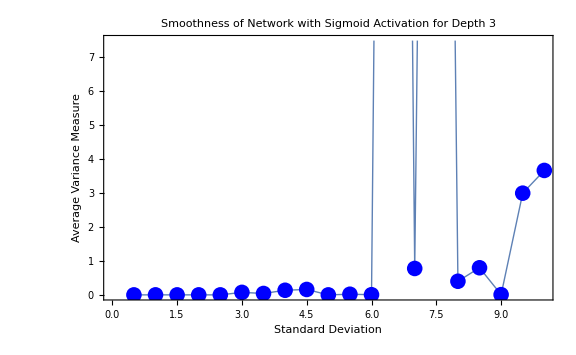

```mathematica
normalPlotVariance[LogisticSigmoid,3,Blue,"Smoothness of Network with Sigmoid Activation for Depth 3"]
```

### Gamma Distributions

The main changes from generating weights with a normal distribution to generating weights with a gamma distribution are that the weights will always be nonnegative in the latter case and that there are now two metrics to examine: α and β instead of just σ.

```mathematica
gammaNetworkPlot[activations_,depths_, alpha_, beta_]:=Module[{netPlots,netInit,f,plots,act,depth},netPlots={{"[◼]", "NetGraphPlot"}}[NetChain[Append[Catenate@Table[{3},#],{}],"Input"->"Real"],EdgeStyle->GrayLevel[.3,.5],EdgeShapeFunction->"Line",ImageSize->Tiny,AspectRatio->1/2]&/@Range[Length[depths]];
SeedRandom[1234];
plots=Append[Prepend[netPlots,""]]@Table[Prepend[Text[act/. Function[x,If[x>0,1,0]]->"Threshold"]]@Table[With[{netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act]},depth],{}],"Input"->"Real"]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->GammaDistribution[alpha,beta],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths}],{act,activations}];
Grid[plots]
]
```

This gammaNetworkPlot function works very similarly to the normalNetworkPlot function, with the key difference coming in the fact that

```mathematica
Rasterize[gammaNetworkPlot[{Function[x,If[x>0,1,0]],Ramp,Tanh,Sin,LogisticSigmoid},{1,2,3,4}, 2, 1]]
```

-Graphics-

As the graph above shows, the gamma distribution has the output maintaining the rough shape of the activation function, with a slight exception for the Sin function. Why is this?
Another question: Why doesn’t Ramp ever lose its gradients with this distribution but does with the normal distribution? Answer: Gamma distributions limit themselves to positive values, and this prevents the Ramp function from ever entering the saturated range where all values go to 0, and the gradient approaches zero. If Ramp is working with positive values only, then the gradient stays at 1, and this also prevents and exploding gradient that would create output graphs with obscene frequencies as can be observed with the Sin function. Now, why does Logistic Sigmoid begin to lose gradients so quickly? Well, while Ramp’s saturated range is for values close to zero, the graph of Logistic Sigmoid shows us that its first derivative approaches 0 for large positive values, which is what initializing weights from a gamma distribution results in. Because of this the gradients almost immediately approach zero, and the Logistic Sigmoid activation function flat-lines faster than it did for a normal distribution. Very similar logic applies for the Thresholding function, but there is another surprising result relating to this specific function in conjunction with the Tanh function. More specifically, why does the Tanh function begin to resemble a thresholding function at higher neural network depths? So, Tanh returns values close to 1 for large positive values and values close to -1 for large negative values. With a higher network depth, we’re applying Tanh again and again, and this pushes the outputs further and further toward one of these two regions, and the network begins to output almost exclusively either 1 or -1. Now why does Sin reach insanely high frequencies? So when we stack multiple layers of a Sin function in a neural network, each layer is processing a linear combination of the outputs of a sin function, and this results in compositions of Sin functions that can lead to harmonics (essentially frequency multipliers). This is what it looks like mathematically:
 


where  represents the matrix of weights at layer  in the neural network and  represents the bias vector at layer .

```mathematica
gammaInitializeNet[alpha_,beta_,activation_,depth_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},depth],{}],"Input"->"Real"],Method->{"Random","Weights"->GammaDistribution[alpha,beta],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
```

```mathematica
gammaEvaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
```

```mathematica
alphas=Range[0.5,5,0.5];
betas=Range[0.5,5,0.5];
gammaMeasureVariance[activation_,depth_]:=Flatten[Table[With[{netInit=gammaInitializeNet[alpha,beta,activation,depth]},{{alpha,beta},Mean[Table[Module[{outputs=gammaEvaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]}],{alpha,alphas},{beta,betas}],1];
gammaMeasureVarianceplotted[activation_,depth_]:=Table[With[{netInit=gammaInitializeNet[alpha,beta,activation,depth]},{alpha,beta,Mean[Table[Module[{outputs=gammaEvaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]}],{alpha,alphas},{beta,betas}];
```

```mathematica
gammaOptimalParams[activation_,depth_]:=Module[{varianceMeasures,minParams,maxParams},varianceMeasures=gammaMeasureVariance[activation,depth];
minParams=varianceMeasures[[First[Ordering[varianceMeasures[[All,2]],1]]]];
maxParams=varianceMeasures[[First[Ordering[varianceMeasures[[All,2]],-1]]]];
{minParams[[1]],maxParams[[1]]}];
```

```mathematica
gammaPlotVariance[activation_,depth_]:=Module[{varianceMeasures,alphaBetaVariance},varianceMeasures=gammaMeasureVarianceplotted[activation,depth];
alphaBetaVariance=Partition[varianceMeasures[[All,3]],Length[betas]];
ListPlot3D[alphaBetaVariance,DataRange->{{First[alphas],Last[alphas]},{First[betas],Last[betas]}},PlotLabel->"Variance Measure for Gamma Distribution",PlotStyle->"Surface",ColorFunction->"Rainbow",InterpolationOrder->2,Mesh->True,ImageSize->Large]];
```

```mathematica
depth=3;
activation=LogisticSigmoid;
gammaOptimalParams[activation,depth]
```

{{2.,4.},{0.5,3.}}

```mathematica
gammaPlotVariance[activation,depth]
```

-Graphics3D-

### Uniform Distribution

Now, the main defining characteristic of weights generated from this distribution is that they will usually be more spread out than those from a normal distribution, or in other words, they will exhibit a higher standard deviation.

```mathematica
uniformNetworkPlot[activations_,depths_,range_]:=Module[{netPlots,netInit,f,plots,act,depth},netPlots={{"[◼]", "NetGraphPlot"}}[NetChain[Append[Catenate@Table[{3},#],{}],"Input"->"Real"],EdgeStyle->GrayLevel[.3,.5],EdgeShapeFunction->"Line",ImageSize->Tiny,AspectRatio->1/2]&/@Range[Length[depths]];
SeedRandom[1234];
plots=Append[Prepend[netPlots,""]]@Table[Prepend[Text[act/. Function[x,If[x>0,1,0]]->"Threshold"]]@Table[With[{netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act]},depth],{}],"Input"->"Real"]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->UniformDistribution[{-range,range}],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths}],{act,activations}];
Grid[plots]
]
```

```mathematica
Rasterize[uniformNetworkPlot[{Function[x,If[x>0,1,0]],Ramp,Tanh,Sin,LogisticSigmoid},{1,2,3,4,5,6,7,8},1]]
```

Obviously, since we are generating the weights from a uniform distribution, any given weight is equally likely to be any number between  and , in this case , -1 and 1. The most striking thing about this collection of output graphs is their flatness. While most of the graphs don’t actually flat-line, their outputs have a much lower frequency than the counterparts that are created by weights initialized from normal or gamma distributions. Why does this happen? Some of the activation functions that we are testing here are non-linear and sensitive to small changes in input (namely Sin). Because the uniform distribution has a lower variance than the normal or gamma distribution, the weights we are initializing will likely have a lower variance than usual, and non-linear functions like Sin or Tanh will be less likely to reach extreme values. Now, the question of whether or not this is a good thing is more complicated. Having these less extreme output graphs lessens the danger of exploding gradients and can stabilize the training process and can be useful in layers that are intended to provide a more predictable output, but on the other hand, having the output graphs be too flat can mean that the neural network won’t be able to fit as well to complex data. At high enough depths (nearer to 10) almost all the activation functions experience gradient loss, so initializing with a uniform distribution doesn’t seem compatible with complex neural network structures.

### Finding Optimal Range to prevent Gradient Loss/Gradient Explosion

```mathematica
uniformInitializeNet[range_,activation_,depth_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},depth],{}],"Input"->"Real"],Method->{"Random","Weights"->UniformDistribution[{-range,range}],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
```

```mathematica
uniformEvaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
```

```mathematica
ranges=Range[0.5,10,0.5];
uniformMeasureVariance[activation_,depth_]:=Table[With[{netInit=uniformInitializeNet[range,activation,depth]},{range,Mean[Table[Module[{outputs=uniformEvaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]}],{range,ranges}];
uniformMeasureVarianceplotted[activation_,depth_]:=Table[With[{netInit=uniformInitializeNet[range,activation,depth]},{range,Mean[Table[Module[{outputs=uniformEvaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]}],{range,ranges}];
```

```mathematica
uniformOptimalRange[activation_,depth_]:=Module[{varianceMeasures,minRange,maxRange},varianceMeasures=uniformMeasureVariance[activation,depth];
minRange=First[varianceMeasures[[First[Ordering[varianceMeasures[[All,2]],1]]]]];
maxRange=First[varianceMeasures[[First[Ordering[varianceMeasures[[All,2]],-1]]]]];
{minRange,maxRange}];
```

```mathematica
depth=3;
activation=LogisticSigmoid;
optimalRanges=uniformOptimalRange[activation,depth];
Print["Optimal Range that Minimizes Variance: ",optimalRanges[[1]]];
Print["Optimal Range that Maximizes Variance: ",optimalRanges[[2]]];
```

```mathematica
uniformPlotVariance[activation_,depth_]:=Module[{varianceMeasures},varianceMeasures=uniformMeasureVarianceplotted[activation,depth];
ListLinePlot[varianceMeasures,Frame->True,FrameLabel->{"Range","Average Variance Measure"},PlotLabel->"Variance Measure for Uniform Distribution",PlotStyle->Thick,Mesh->All,MeshStyle->Blue,ImageSize->Large]];
```

```mathematica
depth=3;
activation=LogisticSigmoid;
uniformPlotVariance[activation,depth]
```

### Special Initializations

Because there are some issues when generating weights from the standard distributions for some activation functions (namely those that resemble Logistic Sigmoid), researchers have come up with a couple of special initializations to enhance the training process when using those functions. This section will generate similar plots for these initializations in a bid to determine whether there are some parameters that when inputted into a Normal, Gamma, or Uniform distribution will perform better than the special initializations.

#### Xavier Initialization

```mathematica
xavierNetworkPlot[activations_,depths_]:=Module[{netPlots,netInit,f,plots,act,depth,fanIn,fanOut,variance},netPlots={{"[◼]", "NetGraphPlot"}}[NetChain[Append[Catenate@Table[{3},#],{}],"Input"->"Real"],EdgeStyle->GrayLevel[.3,.5],EdgeShapeFunction->"Line",ImageSize->Tiny,AspectRatio->1/2]&/@Range[Length[depths]];
SeedRandom[1234];plots=Append[Prepend[netPlots,""]]@Table[Prepend[Text[act/. Function[x,If[x>0,1,0]]->"Threshold"]]@Table[With[{netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act]},depth],{}],"Input"->"Real"]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->With[{fanIn=3,fanOut=3},UniformDistribution[{-Sqrt[6/(fanIn+fanOut)],Sqrt[6/(fanIn+fanOut)]}]],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths}],{act,activations}];
Grid[plots]
]
```

```mathematica
Rasterize[xavierNetworkPlot[{Function[x,If[x>0,1,0]],Ramp,Tanh,Sin,LogisticSigmoid},{1,2,3,4}]]
```

#### He Initialization

```mathematica
heNetworkPlot[activations_,depths_]:=Module[{netPlots,netInit,f,plots,act,depth,fanIn},netPlots={{"[◼]", "NetGraphPlot"}}[NetChain[Append[Catenate@Table[{3},#],{}],"Input"->"Real"],EdgeStyle->GrayLevel[.3,.5],EdgeShapeFunction->"Line",ImageSize->Tiny,AspectRatio->1/2]&/@Range[Length[depths]];
SeedRandom[1234];
plots=Append[Prepend[netPlots,""]]@Table[Prepend[Text[act/. Function[x,If[x>0,1,0]]->"Threshold"]]@Table[With[{netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act]},depth],{}],"Input"->"Real"]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->With[{fanIn=3},NormalDistribution[0,Sqrt[2/fanIn]]],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths}],{act,activations}];
Grid[plots]
]
```

```mathematica
Rasterize[heNetworkPlot[{Function[x,If[x>0,1,0]],Ramp,Tanh,Sin,LogisticSigmoid},{1,2,3,4}]]
```

## Combining Activation Functions to Create More Complex Neural Networks

## Conclusion

## Implications for Future Research

## Bibliography